# Guía de ejercicios M1 U2 - Ley de Coulomb

Este es un notebook hecho por Junior Zambrano para el curso FS-2211 (Física 3) dictado por el profesor Sttiwuer Díaz.

En esta primera parte del código se limpian todas las variables y se definen las funciones que se utilizaran en el resto del notebook. Para correr todo el notebook y así poder cargar en memoria las funciones y las variables correctamente seguir las siguientes instrucciones:

Ir a la sección “Evaluation” de la barra de herramientas.

Seleccionar “Evaluate notebook”.

Observación: la compilación de todo el notebook puede demorar unos segundos.

Limpieza de variables.

```mathematica
Remove["Global`*"];
Clear["Global`*"];
```

Definición de funciones y su descripción (créditos al prof. Sttiwuer Díaz).

Función para la fuerza eléctrica sobre la carga q_f debido a la carga q_i ⟶ F_e[q_f,(r⃗)_f,q_i,(r⃗)_i], donde (r⃗)_i y (r⃗)_f son las posiciones de las carga q_i y q_f, respectivamente.

Función para la magnitud de la fuerza eléctrica sobre las cargas q_1 y q_2 ⟶ MF_e[q_1,q_2,d,K], donde d es la distancia que separa a las cargas q_1 y q_2. Para utilizar el valor K=9 10^9, omitir el argumento K, en caso de K≠9 10^9 indicar su valor en dicho argumento (dejar el valor indicado como constante también es válido, por ejemplo K=K_0).

Función para el campo eléctrico en el punto P debido a la carga q_i ⟶ E_e[(r⃗)_p,q,(r⃗)_q], donde (r⃗)_p y (r⃗)_q son las posiciones del punto P y de la carga q, respectivamente.

```mathematica
Fe[qf_,rf_,qi_,ri_]:=Subscript[K, 0](qf qi)/Norm[rf-ri]^3(rf-ri);
MFe[q1_,q2_,d_,K_:9 10^9]:=Assuming[K>0&&d>0,Refine[Abs[K(q1 q2)/d^2]]];
Ee[rp_,q_,rq_]:=Subscript[K, 0] q/Norm[rp-rq]^3(rp-rq);
```

### Desarrollo:

Se presentan preguntas referentes al Módulo 1 Unidad 2.

#### 1. Planteamiento A:

Para la configuración de dos cargas eléctricas que se muestra en la figura adjunta se tiene que los parámetros a y q son cantidades positivas con dimensiones de longitud y carga eléctrica, respectivamente.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(1a) La intensidad de la fuerza eléctrica entre ambas cargas.
(1b) La componente horizontal de la fuerza eléctrica que actúa sobre la carga negativa.
(1c) La componente vertical de la fuerza eléctrica que actúa sobre la carga positiva.
(1d) La orientación de la fuerza eléctrica que actúa sobre la carga positiva, respecto al eje horizontal positivo.

Solución:

```mathematica
(*Posiciones de las cargas negativa y positiva, respectivamente*)
rq1={0,3a};
rq2={4a,0};
(*Distancia relativa entre ambas cargas*)
d=Assuming[a>0,Refine[Norm[rq2-rq1]]];
"(1a) Magnitud de la fuerza eléctrica"
Assuming[q>0,Refine[MFe[2q,-q,d,Subscript[K, 0]]]]
"(1b) Componente horizontal de la fuerza eléctrica sobre -q"
F1=Assuming[a>0,Refine[Fe[-q,rq1,2q,rq2]]];
F1[[1]]
"(1c) Componente vertical de la fuerza eléctrica sobre 2q"
F2=Assuming[a>0,Refine[Fe[2q,rq2,-q,rq1]]];
F2[[2]]
(*Vector director de la fuerza eléctrica sobre 2q*)
u=F2/PolynomialGCD@@F2;
"(1d) Ángulo en radianes medido desde la horizontal"
VectorAngle[u,{1,0}]//N
Clear[rq1,rq2,d,F1,F2,u];
```

(1a) Magnitud de la fuerza eléctrica

(2 q^2 K_0)/(25 a^2)

(1b) Componente horizontal de la fuerza eléctrica sobre -q

(8 q^2 K_0)/(125 a^2)

(1c) Componente vertical de la fuerza eléctrica sobre 2q

(6 q^2 K_0)/(125 a^2)

(1d) Ángulo en radianes medido desde la horizontal

ArcCos[-4/5]

#### 2. Planteamiento B:

Para la configuración de tres cargas eléctricas que se muestra en la figura adjunta se tiene que los parámetros a y q son cantidades positivas con dimensiones de longitud y carga eléctrica, respectivamente.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(2a) Obtenga la fuerza eléctrica sobre la carga ubicada en el origen del sistema de coordenadas.
(2b) Si las partículas de carga -q y 3q presentan igual masa, calcule la fuerza eléctrica sobre la carga ubicada en el origen suponiendo que la carga neta de las otras dos partículas está ubicada en su centro de masa.
(2c) Si las partículas de carga -q y 3q presentan igual relación de masa (es decir, m y 3m), calcule la fuerza eléctrica sobre la carga ubicada en el origen suponiendo que la carga neta de las otras dos partículas está ubicada en su centro de masa.

Solución:

```mathematica
(*Posiciones de las cargas -q, 2q y 3q, respectivamente*)
rq1={-3a,4a};
rq2={0,0};
rq3={4a,3a};
"(2a) Fuerza eléctrica sobre 2q"
FullSimplify[Assuming[a>0,Refine[Fe[2q,rq2,-q,rq1]+Fe[2q,rq2,3q,rq3]]]]
(*Carga neta de las partículas de carga -q y 3q*)
Q=-q+3q;
(*Posición del centro de masa de las partículas con carga -q y 3q e igual masa m*)
rcm1=(m rq1+m rq2)/(m+m);
"(2b) Fuerza eléctrica sobre 2q debido a la carga especificada"
Assuming[a>0,Refine[Fe[2q,rq2,Q,rcm1]]]
(*Posición del centro de masa de las partículas con carga -q y 3q y de masa m y 3m, respectivamente*)
rcm2=(m rq1+m rq2)/(m+3m);
"(2c) Fuerza eléctrica sobre 2q debido a la carga especificada"
Assuming[a>0,Refine[Fe[2q,rq2,Q,rcm2]]]
Clear[rq1,rq2,rq3,Q,rcm1,rcm2];
```

(2a) Fuerza eléctrica sobre 2q

{-(6 q^2 K_0)/(25 a^2),-(2 q^2 K_0)/(25 a^2)}

(2b) Fuerza eléctrica sobre 2q debido a la carga especificada

{(48 q^2 K_0)/(125 a^2),-(64 q^2 K_0)/(125 a^2)}

(2c) Fuerza eléctrica sobre 2q debido a la carga especificada

{(192 q^2 K_0)/(125 a^2),-(256 q^2 K_0)/(125 a^2)}

#### 3. Planteamiento C:

En los vértices de un triángulo equilátero de lado b se encuentran tres partículas idénticas, cuyos valor de carga es -q. Una cuarta carga positiva Q es colocada sobre el eje de simetría del triángulo y a una altura indicada con la letra y, respecto de la base del triángulo equilátero. Recordar que el eje de simetría es la bisectriz que pasa por el vértice superior y el punto medio entre los dos vértices de la base del triángulo.

-Graphics-

Suponiendo que la coordenada y no puede tomar el valor del vértice superior, responda las siguientes preguntas:

(3a) La fuerza eléctrica que actúa sobre la carga Q debido al sistema de tres cargas negativas, exprese dicho resultado en término de las variables y, Q, b y la constate de Coulomb K en el vacío.
(3b) Encuentre el valor de la variable y para el cual la fuerza eléctrica sobre la carga Q se anule. Compruebe que dicho valor corresponde al baricentro del triángulo (intersección de las tres medianas)
(3c) Obtenga los valores de la coordenada vertical y para que la fuerza sobre la carga positiva Q sea máxima.
(3d) Si la carga Q se coloca en el baricentro del triángulo (intersección de las tres medianas), cual debe ser el valor de dicha carga para que la fuerza resultante sobre cualquier carga -q colocada en el vértice se anule.

Solución:

```mathematica
(*Posiciones de las cargas en los vértices del triángulo y la carga Q*)
rq1={0,0};
rq2={b,0};
rq3={b Cos[π/3],b Sin[π/3]};
rQ={b Cos[π/3],y};
"(3a) Fuerza eléctrica sobre la carga Q debido a las cargas restantes"
FQ=FullSimplify[Assuming[b>0&&b Sin[π/3]>y>0,Refine[Fe[Q,rQ,-q,rq1]+Fe[Q,rQ,-q,rq2]+Fe[Q,rQ,-q,rq3]]]]
"(3b) Valor de y para cuando la fuerza eléctrica total sobre Q es igual a 0"
h=First[Solve[FQ==0,y]]
(*Posición del baricento del triángulo*)
rG={(0+b+b Cos[π/3])/3,(0+0+b Sin[π/3])/3};
"Comprobación que el valor de rQ cuando FQ=0 corresponde al baricentro del triángulo"
(rQ/.h)==rG
"(3c) Valor de y cuando la fuerza eléctrica se hace máxima"

(*Fuerzas eléctricas sobre cada carga en los vértices del triángulo equilátero*)
Fq1=FullSimplify[Assuming[b>0&&b Sin[π/3]>y>0,Refine[Fe[-q,rq1,Q,rG]+Fe[-q,rq1,-q,rq2]+Fe[-q,rq1,-q,rq3]]]];
Fq2=FullSimplify[Assuming[b>0&&b Sin[π/3]>y>0,Refine[Fe[-q,rq2,Q,rG]+Fe[-q,rq2,-q,rq1]+Fe[-q,rq2,-q,rq3]]]];
Fq3=FullSimplify[Assuming[b>0&&b Sin[π/3]>y>0,Refine[Fe[-q,rq3,Q,rG]+Fe[-q,rq3,-q,rq2]+Fe[-q,rq3,-q,rq1]]]];
"(3d) Valor de Q cuando está en en el baricentro del triángulo equilátero para que la fuerza eléctrica en cualquier carga ubicada en los vértices se anule"
Solve[{Fq1==0,Fq2==0,Fq3==0},Q]
Clear[rq1,rq2,rq3,rQ,FQ,h,rG,Fq1,Fq2,Fq3];
```

(3a) Fuerza eléctrica sobre la carga Q debido a las cargas restantes

{0,4 q Q (1/(√3 b-2 y)^2-(4 y)/((b^2+4 y^2)^(3/2))) K_0}

(3b) Valor de y para cuando la fuerza eléctrica total sobre Q es igual a 0

{y→b/(2 √3)}

Comprobación que el valor de rQ cuando FQ=0 corresponde al baricentro del triángulo

True

(3d) Valor de Q cuando está en en el baricentro del triángulo equilátero para que la fuerza eléctrica en cualquier carga ubicada en los vértices se anule

{{Q→q/(√3)}}

#### 4. Planteamiento D:

En la figura adjunta se muestra un triángulo equilátero de lado L y en los vértices del triángulo se han dispuestos tres cargas negativas iguales de valor -q; donde q es una constante positiva con dimensiones de carga. En el baricentro del triángulo se dispone una carga positiva de valor q.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(4a) La fuerza eléctrica sobre la carga ubicada en el punto A, debido a las cargas restantes.
(4b) Si se coloca una quinta carga de valor -2q en el punto medio entre las carga ubicada en la base del triángulo equilátero, determine la fuerza eléctrica sobre dicha carga debido a las cargas restantes.

Solución:

```mathematica
(*Posición de las cargas negativas y la carga positiva (baricentro del triángulo), respectivamente*)
rq1={0,0};
rq2={L,0};
rq3={L Cos[π/3],L Sin[π/3]};
rG={(0+L+L Cos[π/3])/3,(0+0+L Sin[π/3])/3};
"(4a) Fuerza eléctrica sobre la carga en el punto A debido a las cargas restantes"
FullSimplify[Assuming[L>0,Refine[Fe[-q,rq3,-q,rq1]+Fe[-q,rq3,-q,rq2]+Fe[-q,rq3,q,rG]]]]
(*Posición de la nueva carga -2q*)
rq4={L Cos[π/3],0};
"(4b) Fuerza sobre la carga -2q debido a las cargas restantes"
FullSimplify[Assuming[L>0,Refine[Fe[-2q,rq4,-q,rq1]+Fe[-2q,rq4,-q,rq2]+Fe[-2q,rq4,-q,rq3]+Fe[-2q,rq4,q,rG]]]]
Clear[rq1,rq2,rq3,rG,rq4];
```

(4a) Fuerza eléctrica sobre la carga en el punto A debido a las cargas restantes

{0,((-3+√3) q^2 K_0)/L^2}

(4b) Fuerza sobre la carga -2q debido a las cargas restantes

{0,(64 q^2 K_0)/(3 L^2)}

#### 5. Planteamiento E:

En la figura adjunta se muestran cuatro cargas positivas idénticas de carga q dispuestas de forma equidistante entre sí en la parte superior de una circunferencia de radio R. Una quinta carga negativa de valor -2q se encuentra en el punto más bajo de la circunferencia.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(5a) La fuerza eléctrica sobre la carga negativa, debido al resto de cargas positivas.
(5b) Determine la fuerza eléctrica que actúa sobre la carga negativa debido a una carga positiva de valor 4q ubicada en el centro de masa de la distribución discreta de cargas positiva.

Solución:

```mathematica
(*Posición de las cargas positivas y negativa, respectivamente*)
rq1={-R,0};
rq2={-R Cos[π/3],R Sin[π/3]};
rq3={R Cos[π/3],R Sin[π/3]};
rq4={R,0};
rq={0,R};
"(5a) Fuerza eléctrica sobre la carga negativa"
Assuming[R>0,FullSimplify[Refine[Fe[-2q,rq,q,rq1]+Fe[-2q,rq,q,rq2]+Fe[-2q,rq,q,rq3]+Fe[-2q,rq,q,rq4]]]]
(*Posición del centro de masa de la distribución discreta de cargas*)
rcm=(rq1+rq2+rq3+rq4)/4;
"(5b) Fuerza eléctrica sobre la carga negativa debido a la carga especificada"
Cancel[Assuming[R>0,FullSimplify[Refine[Fe[-2q,rq,4q,rcm]]]]]
Clear[rq1,rq2,rq3,rq4,rq,rcm];
```

(5a) Fuerza eléctrica sobre la carga negativa

{0,-(√2 (2+√3) q^2 K_0)/R^2}

(5b) Fuerza eléctrica sobre la carga negativa debido a la carga especificada

{0,-(128 q^2 K_0)/((-4+√3)^2 R^2)}

#### 6. Planteamiento F:

En los vertices de un cuadrado de arista b se encuentran colocadas cuatro cargas según los indicado en la figura adjunta. Considere que el parámetro q es positivo y con dimensiones de carga eléctrica. En la figura también se muestra un sistema de coordenadas cartesiano rectangular cuyo origen se encuentra en la esquina inferior izquierda del cuadrado.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(6a) Calcule la fuerza que actúa sobre las cargas ubicadas en el vértices superior derecho debido al resto de cargas presentes.
(6b) Establezca si la fuerza que actúa sobre las cargas ubicadas en el origen debido a las otras carga es un par acción-reacción de la fuerza obtenida en el inciso anterior.
(6c) Compare la intensidades de la fuerza eléctrica que actúa sobre las carga 2q y la carga ubicada diametralmente opuesta a ésta.

Solución:

```mathematica
(*Posiciones de las cargas positivas*)
rq1={0,0};
rq2={b,0};
rq3={0,b};
rq4={b,b};
"(6a) Fuerza eléctrica sobre la carga en el vértice superior derecho"
Assuming[b>0,FullSimplify[Refine[Fe[q,rq4,q,rq1]+Fe[q,rq4,2q,rq2]+Fe[q,rq4,q,rq3]]]]
"(6b) Fuerza eléctrica sobre la carga en el origen"
Assuming[b>0,FullSimplify[Refine[Fe[q,rq1,2q,rq2]+Fe[q,rq1,q,rq3]+Fe[q,rq1,q,rq4]]]]
(*Magnitud de la fuerza eléctrica sobre q1*)
MF1=Assuming[b>0&&Subscript[K, 0]>0&&q>0,FullSimplify[Refine[Norm[Fe[2q,rq2,q,rq1]+Fe[2q,rq2,q,rq3]+Fe[2q,rq2,q,rq4]]]]];
(*Magnitud de la fuerza eléctrica sobre q2*)
MF2=Assuming[b>0&&Subscript[K, 0]>0&&q>0,FullSimplify[Refine[Norm[Fe[q,rq3,q,rq1]+Fe[q,rq3,2q,rq2]+Fe[q,rq3,q,rq4]]]]];
"(6C) Comparación de las intensidades de las fuerzas"
FullSimplify[MF1/MF2]
Clear[rq1,rq2,rq3,rq4,MF1,MF2];
```

(6a) Fuerza eléctrica sobre la carga en el vértice superior derecho

{((4+√2) q^2 K_0)/(4 b^2),((8+√2) q^2 K_0)/(4 b^2)}

(6b) Fuerza eléctrica sobre la carga en el origen

{-((8+√2) q^2 K_0)/(4 b^2),-((4+√2) q^2 K_0)/(4 b^2)}

(6C) Comparación de las intensidades de las fuerzas

3-√2

7. Cuál es la fuerza que actúa sobre una carga colocada en el centro de un cuadrado de lado a, sabiendo que las cargas en los vertices superiores son iguales a -2q y en los vertices inferiores son iguales a +q. Siendo q una cantidad definida positiva con dimensiones de carga.

Solución:

```mathematica
(*Posiciones de las cargas*)
rq1={0,0};
rq2={a,0};
rq3={0,a};
rq4={a,a};
rC={a/2,a/2};
"Fuerza eléctrica"
Assuming[a>0,FullSimplify[Refine[Fe[Q,rC,q,rq1]+Fe[Q,rC,q,rq2]+Fe[Q,rC,-2q,rq3]+Fe[Q,rC,-2q,rq4]]]]
Clear[rq1,rq2,rq3,rq4,rC];
```

Fuerza eléctrica

{0,(6 √2 q Q K_0)/a^2}

8. Considere la distribución de tres cargas q_1=1μC, q_2=2μC y q_3=-1μC ubicadas en el espacios cuyas coordenada cartesianas (medidas en centímetros) son (0, 0, 1), (0, 0, 0) y (1, 0, 0), respectivamente. Calcule la fuerza eléctrica sobre la carga Q=-2μC ubicada en la coordenada cartesiana (1, 0, 1).

Solución:

```mathematica
(*Posiciones de las cargas*)
rq1={0,0,1};
rq2={0,0,0};
rq3={1,0,0};
rQ={1,0,1};
"Fuerza eléctrica"
FullSimplify[Fe[-2×10^-6,rQ,10^-6,rq1]+Fe[-2×10^-6,rQ,2 10^-6,rq2]+Fe[-2×10^-6,rQ,-10^-6,rq3]/.Subscript[K, 0]->9 10^9]
Clear[rq1,rq2,rq3,rQ];
```

Fuerza eléctrica

{-(9 (2+√2))/1000,0,-(9 (-2+√2))/1000}

9. En las coordenadas cartesianas (a, 0, a), (0, a, 0) y (0, a, a) se encuentran las cargas q_1=Q, q_2=-2Q y q_3=Q, respectivamente. Considera que a es una constante positiva con dimensiones de longitud. Encuentre la fuerza eléctrica sobre la carga q_2 ubicada en el origen, en función de los parámetros del sistema, a saber a, Q y la constante de Coulomb K en el vacío. Discuta como cambiaría la fuerza si la cantidad Q fuese negativa (es decir, Q<0).

Solución:

```mathematica
(*Posiciones de las cargas*)
rq1={a,0,a};
rq2={0,a,0};
rq3={0,a,a};
rq={0,0,0};
"Fuerza eléctrica"
Assuming[a>0,FullSimplify[Refine[Fe[-2Q,rq,Q,rq1]+Fe[-2Q,rq,-2Q,rq2]+Fe[-2Q,rq,Q,rq3]]]]
Clear[rq1,rq2,rq3,rq];
```

Fuerza eléctrica

{(Q^2 K_0)/(√2 a^2),((-8+√2) Q^2 K_0)/(2 a^2),(√2 Q^2 K_0)/a^2}

10. Cuatro cargas q positivas e idénticas se colocan en los vértices de un cuadrado de lado 2a, el cuadrado se encuentra en en plano cartesiano XY según lo indicado en la figura adjunta. En el centro del cuadrado y a una altura igual a la mitad de su arista se ubica una quinta carga negativa, de valor −Q, formando una pirámide.

-Graphics-

Obtenga la fuerza eléctrica que actúa sobre la carga negativa debido a las cargas positivas ubicadas en la base de la pirámide.

Solución:

```mathematica
(*Posición de las cargas puntuales*)
rq1={0,0,0};
rq2={2a,0,0};
rq3={0,2a,0};
rq4={2a,2a,0};
rQ={a,a,a};
"Fuerza eléctrica"
Assuming[a>0,FullSimplify[Refine[Fe[-Q,rQ,q,rq1]+Fe[-Q,rQ,q,rq2]+Fe[-Q,rQ,q,rq3]+Fe[-Q,rQ,q,rq4]]]]
Clear[rq1,rq2,rq3,rq4,rQ]
```

Fuerza eléctrica

{0,0,-(4 q Q K_0)/(3 √3 a^2)}

### Problemas:

#### 1. Planteamiento G:

Dos cargas de igual masa m y de cargas opuestas se encuentran separadas entre sí por una distancia horizontal ℓ. La carga de signo positivo +q está suspendida por un hilo que se desvía de la vertical en un ángulo θ desconocido, mientras que la carga negativa se encuentra a una distancia horizontal de 3ℓ, respecto a la vertical de la carga positiva. Considere que la carga positiva se mantiene en equilibrio debido a el conjunto de fuerzas que actúan sobre la carga.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(1a) Encuentre la tangente del ángulo que forma el hilo con la horizontal.
(1b) Calcule la intensidad de la fuerza normal que ejerce el hilo a la carga positiva.
(1c) Halle el valor de la longitud del hilo, en centímetros, que mantiene suspendida a la carga positiva.

Solución:

```mathematica
(*Sumatoria de fuerzas sobre la carga en el hilo*)
ΣF=Solve[{Fel-T Cos[ϕ]==0,-m g+T Sin[ϕ]==0},{Fel,T}];
(*Magnitudes de la fuerza eléctrica*)
Fel1=Fel/.ΣF[[1]];
Fel2=Assuming[Q>0,Refine[MFe[Q,-Q,ℓ,Subscript[K, 0]]]];
(*Valor de Cot[ϕ]*)
Ctg=Cot[ϕ]/.First[Solve[Fel2==Fel1,Cot[ϕ]]];
"(1a) Valor de Tan[ϕ]"
Tgt=Tan[ϕ]/.First[Solve[1/Ctg==Tan[ϕ],Tan[ϕ]]]
"(1b) Valor de T"
Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&Q>0,FullSimplify[T/.ΣF[[1]]/.ϕ->ArcTan[Tgt]]]
"(1c) Valor de L en cm"
Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&Q>0,FullSimplify[L/.First[Solve[(L Cos[ϕ]/.ϕ->ArcTan[Tgt])==2ℓ,L]]]]×1/100
Clear[ΣF,Fel1,Fel2,Ctg,Tgt,T,L];
```

(11a) Valor de Tan[ϕ]

(g m ℓ^2)/(Q^2 K_0)

(11b) Valor de T

(√(g^2 m^2 ℓ^4+Q^4 K_0^2))/ℓ^2

(11c) Valor de L en cm

1/50 ℓ √(1+(g^2 m^2 ℓ^4)/(Q^4 K_0^2))

#### 2. Planteamiento H:

Dos esferas idénticas de corcho poseen masa m y carga q (desconocida), las cuales están suspendida mediante hilos de longitud ℓ tal como se indica en cada figura adjunta. Los hilos se encuentran unidos al techo y están separados entre si por una longitud igual a d, según lo indicado en la figura. Debido a la repulsión eléctrica ambos hilos se desvía de la vertical en un ángulo θ y luego se mantienen en equilibrio.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(2a) Obtenga el valor de la carga en términos de los parámetros d, ℓ, θ, m, g, y la constante de Coulomb K, en el vacío.
(2b) Si los hilos se encuentran atados al techo en un mismo punto, demuestre que la deflexion de los hilos es exactamente π/4 cuando los valores de carga, masa y longitud vienen dados por 1 10^-4C, m=18Kg y ℓ=0.5m, respectivamente.

Solución:

```mathematica
(*Sumatoria de fuerzas sobre la carga izquierda*)
ΣF=Solve[{-Fel+T Sin[θ]==0,-m g+T Cos[θ]==0},{Fel,T}];
(*Magnitudes de la fuerza eléctrica*)
Fel1=Fel/.ΣF[[1]];
Fel2=Assuming[q>0,Refine[MFe[q,q,d+2ℓ Sin[θ],Subscript[K, 0]]]];
"(12a) Valor de la carga eléctrica"
Carga=q/.Last[Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&q>0,FullSimplify[Solve[Fel1==Fel2,q]]]]
"(12b) Ángulo de deflexión de los hilos"
First[Solve[q==Carga,θ]/.{g->10,m->18,ℓ->5 10^-1,Subscript[K, 0]->9 10^9,d->0,q->1 10^-4}]
Clear[ΣF,Fel1,Fel2,Carga];
```

(12a) Valor de la carga eléctrica

(d+2 ℓ Sin[θ]) √((g m Tan[θ])/K_0)

(12b) Ángulo de deflexión de los hilos

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{θ→π/4}

3. Dos bloques de masa m y carga Q (desconocida), se encuentran sobre una mesa horizontal sin fricción, unidos mediante un resorte de constante elástica k_0. Cuando los bloques están descargados, el resorte se encuentra en su longitud natural ℓ_0 tal como se indica en la figura adjunta. Si los bloques adquieren carga Q, entonces el resorte se estira hasta una longitud 2 ℓ_0 cuando alcanzar su nueva posición de equilibrio.

-Graphics-

(a) Determine cuanto se desplaza cada bloque después de adquirir la carga Q.
(b) Obtenga una expresión para la carga Q en función de los datos.

Solución:

```mathematica
(*Posición inicial del bloque derecho con origen de coordenadas en el punto medio de la distancia que separa ambos bloques*)
ri={0,Subscript[ℓ, 0]/2};
(*Posición final*)
rf={0,Subscript[ℓ, 0]};
"(a) Diferencia de distancias"
Assuming[Subscript[ℓ, 0]>0,Refine[Norm[rf-ri]]]
(*Sumatoria de fuerzas sobre el bloque derecho*)
ΣF=Solve[Fel-Subscript[k, 0] Subscript[ℓ, 0]/2==0,Fel];
(*Magnitudes de las fuerzas eléctricas*)
Fel1=Fel/.ΣF[[1]];
Fel2=Assuming[Q>0,Refine[MFe[Q,Q,2 Subscript[ℓ, 0],Subscript[K, 0]]]]/.Subscript[K, 0]->1/(4π Subscript[ϵ, 0]);
"(b) Valor de la carga eléctrica"
Last[Assuming[Subscript[ℓ, 0]>0&&Subscript[k, 0]>0&&Subscript[ϵ, 0]>0,FullSimplify[Solve[Fel1==Fel2,Q]]]]
Clear[ri,rf,ΣF,Fel1,Fel2];
```

(a) Diferencia de distancias

ℓ_0/2

(b) Valor de la carga eléctrica

{Q→2 √(2 π) √(k_0 ℓ_0^3 ϵ_0)}

4. Dos cargas idénticas q, se encuentran fijas sobre una mesa horizontal y separadas a una distancia de 2a, el valor de a es desconocido. Una tercera esfera de masa m y carga q es capaz de deslizar, sin fricción, por un barra aislante colocada rígidamente en la vertical, la cual pasa por el punto medio entre las dos cargas ubicadas en la mesa. Debido a la repulsión eléctrica entre las cargas, la esfera se encuentra inicialmente a una altura h por encima de la mesa tal como se muestra en la figura.

-Graphics-

(a) Obtenga una expresión para la fuerza ejercidas por las cargas sobre la esfera, en función de q, h, a y la constante eléctrica K.
(b) Encuentre una expresión para la distancia a cuando la esfera alcanza por encima de la mesa el equilibrio, exprese el resultado en función de q, h y la constante eléctrica K.
(c) Para que valores de h, la fuerza sobre la esfera se hace máxima o mínima.

Solución:

```mathematica
(*Posición de las cargas puntuales*)
rq1={-a,0};
rq2={a,0};
rq={0,h};
"(a) Fuerza eléctrica sobre la esfera"
F=Assuming[q>0&&a>0&&h>0,FullSimplify[Fe[q,rq,q,rq1]+Fe[q,rq,q,rq2]]]
(*Sumatoria de fuerzas sobre la esfera cuando se alcanza el equilibro electrostático*)
ΣF=Solve[-m g + Fel==0,Fel]
"(b) Expresión para a cuando la esfera alcanza el equilibro electrostático"
Last[Assuming[g>0&&m>0&&h>0&&q>0&&Subscript[K, 0]>0&&Elem,FullSimplify[Solve[F[[2]]==(Fel/.ΣF[[1]]),a]]]]
(*Estudio de los puntos críticos de F*)
PtoCritF=Solve[D[F,h]==0,h];
"(c) Valor de h cuando F se hace máxima"
PtoCritF[[2]]
Clear[rq1,rq2,rq,F,ΣF,PtoCritF];
```

(a) Fuerza eléctrica sobre la esfera

{0,(2 h q^2 K_0)/((a^2+h^2)^(3/2))}

{{Fel→g m}}

(b) Expresión para a cuando la esfera alcanza el equilibro electrostático

{a→√(h (-h+2^(2/3) ((q^4 K_0^2)/(g^2 h m^2))^(1/3)))}

(c) Valor de h cuando F se hace máxima

{h→a/(√2)}

5. En una taza de cerámica posee en su interior una forma de arco de parábola, cuya ecuación queda descrita por y=x^2/b . Dos cuerpos de igual masa m y carga q, se encuentran a la misma altura b en el interior de la taza, bajo la acción del campo gravitacional terrestre, tal como se ilustra en la figura adjunta.

-Graphics-

(a) Determine que ambas masas se encuentran separadas por una distancia igual a 2b.
(b) Encuentre el valor de la carga eléctrica para que el sistema se mantenga en reposo, exprese su resultado en función de los parámetros m, g, b y la constante eléctrica.

Solución:

```mathematica
"(a) Distancia de separación entre las cargas"
Refine[Abs[2x]/.First[Solve[b==x^2/b,x]],b>0]
(*Sumatoria de fuerzas en la carga izquierda*)
ΣF=Solve[{-Fel+Fn Cos[θ]==0,-m g+Fn Sin[θ]==0},{Fel,Fn}];
(*Magnitudes de las fuerzas eléctricas*)
Fel1=Fel/.ΣF[[1]];
Fel2=Assuming[q>0,Refine[MFe[q,q,2b,Subscript[K, 0]]]];
(*Carga eléctrica sin valor de la Cot[θ]*)
Carga=q/.Last[Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&q>0,FullSimplify[Solve[Fel1==Fel2,q]]]];
(*Valor de y dada la ecuación de la curva*)
y=x^2/b;
(*Derivada de y para hallar la pendiente de la recta tangente a la curva*)
Ty=D[y,x];
(*Pendiente de la recta normal a la tangente y valor de la Tan[θ]*)
Ny=-1/Ty;
(*Cuando se sustituye la Tan[θ] en el valor de la carga, se cambia el valor de x por el de la componente horizontal de la posición de la carga*)
"(b) Carga eléctrica"
Carga/.Cot[θ]->1/Ny/.x->-b
Clear[ΣF,Fel1,Fel2,Carga,y,Ty,Ny];
```

(a) Distancia de separación entre las cargas

2 b

(b) Carga eléctrica

2 √2 b √((g m)/K_0)

Gráfica de la parábola y las rectas tangente y normal a x con x=-1∧b=1

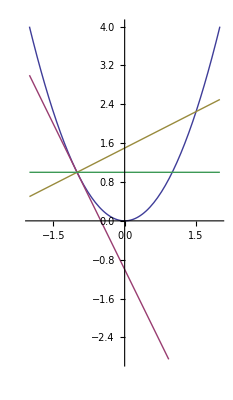

```mathematica
"Gráfica de la parábola y las rectas tangente y normal a x con x=-1∧b=1"
EP=x^2;
px=-1;
py=x^2/.x->-1;
mt=D[x^2/b,x]/.{x->px,b->1};
mn=-1/D[x^2/b,x]/.{x->px,b->1};
rt=mt(x-px)+py;
rn=mn(x-px)+py;
Plot[{EP,rt,rn,py},{x,-2,2},AspectRatio->Automatic]
Clear[EP,px,py,mt,mn,rt,rn];
```

6. Tres partículas idénticas, de masa m y cargadas con carga q>0, cuelgan de un techo mediante hilos aislantes tal como se ilustra en la
figura. Cuando las cargas se ubican en los vértices de un cuadrado de lado ℓ, el sistema permanece en equilibrio. En presencia del campo gravitacional terrestre responda:

-Graphics-

(a) ¿Cuál es el valor de la carga q?
(b) Determine la tensión ejercida por el hilo que se encuentra vertical.

Solución:

```mathematica
(*Posiciones de las cargas con el origen de coordenadas en el punto de contacto del hilo del medio con el techo*)
rq1={0,0};
rq2={ℓ Sin[π/4],-ℓ Cos[π/4]};
rq3={2ℓ Sin[π/4],0};
(*Sumatoria de fuerzas en la carga izquierda*)
ΣF=Solve[{-Fel Cos[θ]-Fel/2+T1 Cos[θ]==0,Fel Sin[θ]-m g+T1 Sin[θ]==0,-Fel Cos[θ]-Fel Cos[θ]-m g+T2==0},{Fel,T1,T2}]/.θ->π/4;
(*Magnitudes de las fuerzas eléctricas*)
Fel1=Fel/.ΣF[[1]];
Fel2=Assuming[ℓ>0&&q>0&&Subscript[K, 0]>0,FullSimplify[Norm[Fe[q,rq1,q,rq2]]]];
"(a) Valor de la carga eléctrica"
Carga=q/.Last[Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&q>0,FullSimplify[Solve[Fel1==Fel2,q]]]]
"(b) Tensión del hilo vertical"
FullSimplify[T2/.ΣF[[1]]]
Clear[rq1,rq2,rq3,ΣF,Fel1,Fel2,Carga];
```

(a) Valor de la carga eléctrica

√2 ℓ √((g m)/(K_0+2 √2 K_0))

(b) Tensión del hilo vertical

1/7 (15-2 √2) g m

7. Una esfera de masa m, con carga positiva Q, está suspendida mediante un hilo aislante de longitud ℓ, en presencia del campo gravitacional terrestre. Otra esfera con carga negativa -Q se encuentra a la derecha de la primera y a una distancia horizontal de longitud ℓ tal como se muestra en la figura de abajo.

-Graphics-

(a) Calcule el ángulo para el cual se inclina la carga positiva, así como la posición (x, y) indicadas.
(b) Encuentre el lugar, sobre la recta que conecta a las cargas, donde se deba colocar una tercera carga negativa -2Q para que la esfera con carga positiva se mantenga suspendida verticalmente.

Solución:

```mathematica
(*Sumatoria de fuerzas sobre la carga izquierda*)
ΣF=Solve[{Fel-T Sin[θ]==0,-m g+T Cos[θ]==0},{Fel,T}];
(*Magnitudes de la fuerza eléctrica*)
Fel1=Fel/.ΣF[[1]];
Fel2=Assuming[Q>0,Refine[MFe[Q,-Q,ℓ ,Subscript[K, 0]]]];
"(a) Ángulo θ"
Angulo=θ-π C[1]/.Normal[First[Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&q>0&&π/2>θ>0,FullSimplify[Solve[Fel1==Fel2,θ]]]]]
First[Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&q>0&&π/2>θ>0,FullSimplify[Solve[x==ℓ Sin[Angulo],x]]]]
First[Assuming[g>0&&m>0&&ℓ>0&&Subscript[K, 0]>0&&q>0&&π/2>θ>0,FullSimplify[Solve[y==ℓ -ℓ Cos[Angulo],y]]]]
(*Magnitud de la fuerza eléctrica entre -2Q y Q*)
Fel3=Assuming[Q>0,Refine[MFe[Q,-2Q,L,Subscript[K, 0]]]];
(*Magnitud de la fuerza eléctrica entre -Q y Q con la nueva distancia*)
Fel4=Assuming[Q>0,Refine[MFe[Q,-Q,FullSimplify[√((ℓ Sin[θ]+ℓ)^2+(ℓ-ℓ Cos[θ])^2)],Subscript[K, 0]]]];
(*Igualamos las magnitudes de las fuerza eléctricas que actúan sobre Q*)
d=Assuming[π/2>θ>0,FullSimplify[Solve[Fel3==Fel4,L]]];
"(b) distancia de -2Q para que el hilo de Q quede vertical"
L/.d[[1]]
Clear[ΣF,Fel1,Fel2,Angulo,Fel3,Fel4,d];
```

(a) Ángulo θ

ArcCot[(g m ℓ^2)/(Q^2 K_0)]

{x→(Q^2 ℓ K_0)/(√(g^2 m^2 ℓ^4+Q^4 K_0^2))}

{y→ℓ-ℓ/(√(1+(Q^4 K_0^2)/(g^2 m^2 ℓ^4)))}

(b) distancia de -2Q para que el hilo de Q quede vertical

ℓ √(6-4 Cos[θ]+4 Sin[θ])

## Distribución continua: Módulo 3 Unidad 2

### Selección simple:

Se presentan preguntas de selección simple referentes al Módulo 1 Unidad 2.

#### Planteamiento 1

En la figura adjunta se muestra un alambre recto de longitud 2a y con una densidad local λ_*=Q Sin[θ], donde Q es una constante positiva con dimensiones de carga eléctrica y θ es la posición angular medida desde la vertical, según los indicado en la figura. Considere que un incremento infinitesimal de esta posición angular dθ contiene un elemento infinitesimal de carga dQ dispuesto horizontalmente. Tenga en cuenta que la “densidad local λ_*=dq/dθ. A la mitad del alambre y por debajo de éste, a una distancia a, se encuentra una partícula con carga positiva Q en el origen del sistema de coordenadas.

-Graphics-

Sobre la base de este planteamiento responda las siguientes preguntas:

(1a) La carga que tiene el alambre viene dada por:

Solución:

```mathematica
FullSimplify[2×Integrate[Q Sin[θ],{θ,0,π/4}]]
```

-(-2+√2) Q

(1b) La fuerza que ejerce el alambre sobre la carga ubicada en el origen viene dada por:

Solución:

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rQ={0,0};
rdq={a Tan[θ],a};
(*Diferencial de carga de la forma dq=λ_*dθ*)
dq=Q Sin[θ];
"Diferencial de Fuerza Eléctrica"
dF=FullSimplify[Assuming[a>0&&π/4≥θ≥0,Refine[Fe[Q,rQ,dq,rdq]]]]
"Fuerza Eléctrica"
F=FullSimplify[Assuming[a>0,Integrate[dF,{θ,-π/4,π/4}]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rQ,rdq,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{-(a Q^2 Sin[θ] K_0 Tan[θ])/((a^2 Sec[θ]^2)^(3/2)),-(a Q^2 Sin[θ] K_0)/((a^2 Sec[θ]^2)^(3/2))}

Fuerza Eléctrica

{-(π Q^2 K_0)/(16 a^2),0}

Factorizando

{-(π Q^2 K_0)/(16 a^2),{1,0}}

(1c) Encuentre la distribución de carga a lo largo de la longitud de la barra en términos de la coordenada angular θ:

Solución:

Recordemos que ds=𝓋 dθ, donde 𝓋 es la magnitud de la derivada de la posición del diferencial de carga. De esa relación obtenemos dθ/ds=1/𝓋. Tenemos que la densidad de carga por regla de la cadena es:

λ(s) = dq/dθ dθ/ds=λ_*dθ/ds=λ_*1/𝓋⇒λ(s)=Q Sin[θ]1/𝓋

```mathematica
(*Posición del diferencial de carga*)
rdq={a Tan[θ],a};
"Magnitud de la tasa de cambio de la posición del diferencial de carga"
𝓋=Assuming[π/4≥θ≥0&&a>0,Refine[Norm[D[rdq,θ]]]]
"Densidad de carga lineal λ(s)"
Q Sin[θ]/𝓋
Clear[rdq,𝓋];
```

Magnitud de la tasa de cambio de la posición del diferencial de carga

a Sec[θ]^2

Densidad de carga lineal λ(s)

(Q Cos[θ]^2 Sin[θ])/a

#### Planteamiento 2

Una barra aislante delgada se dobla en forma de una circunferencia de radio R. La carga sobre la barra no se distribuye de manera uniforme, presentando una densidad local lineal de carga dada por la función matemática λ(θ)=λ_0 Sin[θ] donde λ_0 es una constante positiva con dimensiones de carga por unidad de longitud, mientras que θ es la coordenada polar, medida desde el semi-eje horizontal positivo, tal como se indica en la figura adjunta. Sobre la base de este planteamiento responda las siguientes preguntas:

-Graphics-

2. Cuál de las siguientes afirmaciones es la correcta:

Solución:

```mathematica
"Semi-aro superior"
Integrate[Subscript[λ, 0] Sin[θ]R,{θ,0,π}]
"Semi-aro inferior"
Integrate[Subscript[λ, 0] Sin[θ]R,{θ,π,2π}]
```

Semi-aro superior

2 R λ_0

Semi-aro inferior

-2 R λ_0

3. El campo eléctrico en el centro del anillo viene dado por:

Solución:

```mathematica
(*Posición del punto y del diferencial de carga, respectivamente*)
rp={0,0};
rdq={R Cos[θ],R Sin[θ]};
dq=Subscript[λ, 0] Sin[θ]R;
"Diferencial de Fuerza Eléctrica"
dE=PowerExpand[FullSimplify[Assuming[R>0&&π/2>θ>0,Refine[Ee[rp,dq,rdq]]]]]
"Fuerza Eléctrica"
CE=Integrate[dE,{θ,0,2π}]/.Subscript[K, 0]->1/(4 π Subscript[ϵ, 0])
"Factorizando"
{PolynomialGCD@@CE,CE/PolynomialGCD@@CE}
Clear[rp,rdq,dq,dE,CE];
```

Diferencial de Fuerza Eléctrica

{-(Cos[θ] Sin[θ] K_0 λ_0)/R,-(Sin[θ]^2 K_0 λ_0)/R}

Fuerza Eléctrica

{0,-λ_0/(4 R ϵ_0)}

Factorizando

{-λ_0/(4 R ϵ_0),{0,1}}

### Desarrollo:

Se presentan preguntas referentes al Módulo 3 Unidad 2.

1. Una barra de longitud L y carga negativa -Q distribuida en toda su longitud tiene una densidad lineal del carga λ(s) proporcional a la longitud s, siendo ésta longitud la indicada en la figura adjunta. En un incremento infinitesimal de ésta longitud hay contenida una carga infinitesimal dq. Por otra parte, en el extremo izquierdo de la barra y a una altura y≠0 se encuentra una carga puntual q_0.

-Graphics-

Calcule la fuerza eléctrica que ejerce la barra sobre la carga puntual.

Solución: Tenemos que λ(s)∝s⇒λ(s)=λ_0 s. Para hallar λ_0 integramos sabiendo que la carga se distribuye por toda la barra, es decir, dq=λ(s)ds⇒∫_0^-Q ⅆq=∫_0^L λ(s)ⅆs⇒-Q=∫_0^L λ_0 sⅆs y despejamos λ_0. Luego sustituimos ese valor de λ_0 en λ(s) para hallar la densidad de carga lineal.

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rq0={0,y};
rdq={s,0};
(*Densidad de carga lineal no uniforme dada por λ(s)∝s⇒λ(s)=Subscript[λ, 0] s*)
λs=λ0 s/.First[Solve[-Q==Integrate[λ0 s,{s,0,L}],λ0]];
(*Diferencial de carga de la forma dq=λ(s)ds*)
dq=λs ;
"Diferencial de Fuerza Eléctrica"
dF=Assuming[L>s>0&&y>0,Refine[Fe[q0,rq0,dq,rdq]]]
"Fuerza Eléctrica"
F=Cancel[FullSimplify[Assuming[L>0&&y>0,Integrate[dF,{s,0,L}]]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rq0,rdq,λs,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{(2 Q q0 s^2 K_0)/(L^2 (s^2+y^2)^(3/2)),-(2 Q q0 s y K_0)/(L^2 (s^2+y^2)^(3/2))}

Fuerza Eléctrica

{-(2 Q q0 (L-√(L^2+y^2) ArcSinh[L/y]) K_0)/(L^2 √(L^2+y^2)),-(2 Q q0 (-y+√(L^2+y^2)) K_0)/(L^2 √(L^2+y^2))}

Factorizando

{(2 Q q0 K_0)/(L^2 √(L^2+y^2)),{-L+√(L^2+y^2) ArcSinh[L/y],y-√(L^2+y^2)}}

2. Resuelva el problema del inciso anterior considerando que la carga de la barra se encuentra distribuida de manera uniforme.

Solución:

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rq0={0,y};
rdq={s,0};
(*Diferencial de carga de la forma dq=⟨λ⟩ds*)
dq=-Q/L ;
"Diferencial de Fuerza Eléctrica"
dF=Assuming[L>s>0&&y>0,Refine[Fe[q0,rq0,dq,rdq]]]
"Fuerza Eléctrica"
F=Cancel[FullSimplify[Assuming[L>0&&y>0,Integrate[dF,{s,0,L}]]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rq0,rdq,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{(Q q0 s K_0)/(L (s^2+y^2)^(3/2)),-(Q q0 y K_0)/(L (s^2+y^2)^(3/2))}

Fuerza Eléctrica

{(Q q0 (-y+√(L^2+y^2)) K_0)/(L y √(L^2+y^2)),-(Q q0 K_0)/(y √(L^2+y^2))}

Factorizando

{(Q q0 K_0)/(L y √(L^2+y^2)),{-y+√(L^2+y^2),-L}}

3. Una lámina cuya base es de longitud 2L y alto L presenta una carga negativa -Q distribuida uniformemente en toda su superficie, siendo ésta longitud la indicada en la figura adjunta. Un incremento infinitesimal del parámetro vertical u hay contenida una carga infinitesimal dq en el área dA, la cual está formada por una franja de longitud 2L y altura du. Por otra parte, sobre el eje vertical y a una altura y>L se encuentra una carga puntual positiva q_0.

-Graphics-

Calcule la fuerza eléctrica que ejerce la lámina sobre la carga puntual.

Solución: Hallaremos la fuerza eléctrica a través de dos métodos:

Método 1: definiendo la posición de dq tal que su componente horizontal varíe entre 0 y 2L (longitud de la placa), su componente vertical varíe entre 0 y L (altura de la placa) y cuyo diferencial de área sea dA=dldu, donde l corresponde a la variable horizontal antes mencionada y u a la variable vertical.

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rq0={0,y};
rdq={l,u};
(*Diferencial de carga de la forma dq=⟨λ⟩dA=⟨λ⟩dldu*)
dq=-Q/(2L×L);
"Diferencial de Fuerza Eléctrica"
dF=Cancel[Assuming[y>L>u>0&&l>0,Refine[Fe[q0,rq0,dq,rdq]]]]
"Fuerza Eléctrica"
F=Cancel[FullSimplify[Assuming[y>L>0&&u>0&&l>0,Integrate[dF,{u,0,L},{l,0,2L}]]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rq0,rdq,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{(l Q q0 K_0)/(2 L^2 (l^2+u^2-2 u y+y^2)^(3/2)),(Q q0 (u-y) K_0)/(2 L^2 (l^2+u^2-2 u y+y^2)^(3/2))}

Fuerza Eléctrica

{(Q q0 Log[(y (y-√(4 L^2+y^2)))/((L-y) (L-y+√(5 L^2-2 L y+y^2)))] K_0)/(2 L^2),(Q q0 Log[((-L+y) (2 L+√(4 L^2+y^2)))/(y (2 L+√(5 L^2-2 L y+y^2)))] K_0)/(2 L^2)}

Factorizando

{(Q q0 K_0)/(2 L^2),{Log[(y (y-√(4 L^2+y^2)))/((L-y) (L-y+√(5 L^2-2 L y+y^2)))],Log[((-L+y) (2 L+√(4 L^2+y^2)))/(y (2 L+√(5 L^2-2 L y+y^2)))]}}

Método 2: partiendo de la fuerza eléctrica que obtuvimos del ejercicio anterior. Como la placa, en comparación con la barra, varía en altura y no en longitud y la carga q_0 está ubicada en una posición similar a la del ejercicio anterior, entonces podemos integrar un nuevo diferencial de fuerza respecto a un parámetro u que varíe entre 0 y L (altura de la placa) y hacemos los cambios de variable necesarios en la fuerza eléctrica sobre la carga q_0 del ejercicio anterior para adapatarla a los datos presentados en el problema.

```mathematica
(*Diferencial de carga de la forma dq=⟨λ⟩2Ldu*)
dq=-Q/(2L×L)2L;
"Diferencial de Fuerza Eléctrica"
dF=Cancel[FullSimplify[{(Q q0 (-y+√(L^2+y^2)) Subscript[K, 0])/(L y √(L^2+y^2)),-(Q q0 Subscript[K, 0])/(y √(L^2+y^2))}/.{Q->-dq,L->2 L,y->y-u}]]
"Fuerza Eléctrica"
F=Cancel[FullSimplify[Assuming[y>L>u>0,Integrate[dF,{u,0,L}]]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{-(Q q0 (u-y+√(4 L^2+u^2-2 u y+y^2)) K_0)/(2 L^2 (u-y) √(4 L^2+u^2-2 u y+y^2)),(Q q0 K_0)/(L (u-y) √(4 L^2+u^2-2 u y+y^2))}

Fuerza Eléctrica

{(Q q0 Log[(y (y-√(4 L^2+y^2)))/((L-y) (L-y+√(5 L^2-2 L y+y^2)))] K_0)/(2 L^2),(Q q0 Log[((-L+y) (2 L+√(4 L^2+y^2)))/(y (2 L+√(5 L^2-2 L y+y^2)))] K_0)/(2 L^2)}

Factorizando

{(Q q0 K_0)/(2 L^2),{Log[(y (y-√(4 L^2+y^2)))/((L-y) (L-y+√(5 L^2-2 L y+y^2)))],Log[((-L+y) (2 L+√(4 L^2+y^2)))/(y (2 L+√(5 L^2-2 L y+y^2)))]}}

4. Una barra de longitud L tiene una carga negativa -Q distribuida uniformemente en toda su longitud, la barra se encuentra horizontal y con su extremo izquierdo en el origen del sistema de coordenadas cartesianas. Sea s el parámetro que mide la longitud de los puntos sobre la barra respecto al origen del sistema de coordenadas, un incremento infinitesimal de ésta longitud ds tiene contenido un elemento infinitesimal de carga dq. Por otra parte, en el extremo derecho de la barra y a una distancia d se encuentra una carga puntual q_0.

-Graphics-

Calcule la fuerza eléctrica que ejerce la barra sobre la carga puntual.

Solución:

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rq0={L+h,0};
rdq={s,0};
(*Diferencial de carga de la forma dq=⟨λ⟩ds*)
dq=-Q/L;
"Diferencial de Fuerza Eléctrica"
dF=Cancel[Assuming[L>s>0&&h>0,Refine[Fe[q0,rq0,dq,rdq]]]]
"Fuerza Eléctrica"
F=Cancel[FullSimplify[Integrate[dF,{s,0,L}],{L>s>0,h>0}]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rq0,rdq,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{-(Q q0 K_0)/(L (h+L-s)^2),0}

Fuerza Eléctrica

{-(Q q0 K_0)/(h (h+L)),0}

Factorizando

{-(Q q0 K_0)/(h (h+L)),{1,0}}

5. En la figura adjunta se muestra un alambre en forma de un arco de circunferencia de radio R. El alambre tiene una carga Q distribuida en todo el alambre de manera uniforme. Considere al parámetro θ como la posición angular positiva medida respecto al semieje horizontal negativo, de manera que un incremento infinitesimal de esta coordenada contiene un elemento infinitesimal de carga dq, según lo indicado en la figura adjunta. Una carga puntual q_0 está ubicada en el origen del sistema de coordenadas.

-Graphics-

Encuentre la fuerza eléctrica sobre la carga puntual debida al arco de circunferencia.

Solución:

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rq0={0,0};
rdq={R Cos[θ],R Sin[θ]};
(*Diferencial de carga de la forma dq=⟨λ⟩rdθ*)
dq=Q/((2π R)/4) R;
"Diferencial de Fuerza Eléctrica"
dF=Cancel[FullSimplify[Assuming[R>0&&π/2≥θ≥0,Refine[Fe[q0,rq0,dq,rdq]]]]]
"Fuerza Eléctrica"
F=Cancel[Assuming[R>0,Integrate[dF,{θ,0,π/2}]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rq0,rdq,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{-(2 Q q0 R Cos[θ] K_0)/(π (R^2)^(3/2)),-(2 Q q0 R Sin[θ] K_0)/(π (R^2)^(3/2))}

Fuerza Eléctrica

{-(2 Q q0 K_0)/(π R^2),-(2 Q q0 K_0)/(π R^2)}

Factorizando

{(2 Q q0 K_0)/(π R^2),{-1,-1}}

6. En la figura adjunta se muestra un sector circular de radio interior b y radio exterior a, dicho sector tiene una carga negativa -Q distribuida uniformemente. Considere el parámetro r como la distancia radial medida respecto al origen del sistema de coordenadas cartesiano, de manera que un incremento infinitesimal de esta coordenada contiene un elemento infinitesimal de carga dq, según lo indicado en la figura adjunta. Una carga puntual positiva q_0 está ubicada en el origen del sistema de coordenadas.

-Graphics-

Encuentre la fuerza eléctrica sobre la carga puntual debida al sector circular.

Solución: Hallaremos la fuerza eléctrica a través de dos métodos:

Método 1: definiendo la posición de dq tal que su componente horizontal r Cos[θ] varíe entre 0 y π/2, su componente vertical r Sin[θ] varíe también 0 y π/2 y cuyo diferencial de área sea dA=rdθdr, donde θ corresponde al ángulo medido desde la horizontal y r el radio del segmento circular que varía entre b y a.

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rq0={0,0};
rdq={r Cos[θ] ,r Sin[θ]};
(*Área del segmento circular de radio a y de radio b indicados en la figura, respectivamente*)
Aa=π/4 a^2;
Ab=π/4 b^2;
(*Diferencial de carga de la forma dq=⟨λ⟩dA=⟨λ⟩rdθdr*)
dq=-Q/(Aa-Ab)r;
"Diferencial de Fuerza Eléctrica"
dF=Cancel[FullSimplify[Fe[q0,rq0,dq,rdq],{a>b>0,r>0,π/2≥θ≥0}]]
"Fuerza Eléctrica"
F=Cancel[FullSimplify[Assuming[a≠b&&a>b>0,Integrate[dF,{r,b,a},{θ,0,π/2}]]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rq0,rdq,Aa,Ab,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{(4 Q q0 Cos[θ] K_0)/((a^2-b^2) π r),(4 Q q0 Sin[θ] K_0)/((a^2-b^2) π r)}

Fuerza Eléctrica

{(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π),(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π)}

Factorizando

{(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π),{1,1}}

Método 2: partiendo de la fuerza eléctrica que obtuvimos del ejercicio anterior. Como el segmento circular, en comparación con el segmento de aro, varía en radio y no en desplazamiento angular y la carga q_0 está ubicada en la misma posición a la del ejercicio anterior, entonces podemos integrar un nuevo diferencial de fuerza respecto a un parámetro r que varíe entre b y a (radio mínimo y máximo del segmento circular, respectivamente) y hacemos los cambios de variable necesarios en la fuerza eléctrica sobre la carga q_0 del ejercicio anterior para adapatarla a los datos presentados en el problema.

Diferencial de Fuerza Eléctrica

{(4 Q q0 Cos[θ] K_0)/((a^2-b^2) π r),(4 Q q0 Sin[θ] K_0)/((a^2-b^2) π r)}

Fuerza Eléctrica

{(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π),(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π)}

Factorizando

{(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π),{1,1}}

```mathematica
(*Área del segmento circular de radio a y de radio b indicados en la figura, respectivamente*)
Aa=π/4 a^2;
Ab=π/4 b^2;
(*Diferencial de carga de la forma dq=⟨λ⟩r π/2 dr*)
dq=-Q/(Aa-Ab)π/2 r;
"Diferencial de Fuerza Eléctrica"
dF=Cancel[FullSimplify[{-(2 Q q0 Subscript[K, 0])/(π R^2),-(2 Q q0 Subscript[K, 0])/(π R^2)}/.{Q->dq,R->r}]]
"Fuerza Eléctrica"
F=Cancel[FullSimplify[Assuming[a≠b&&a>b>0,Integrate[dF,{r,b,a}]]]]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[Aa,Ab,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{(4 Q q0 K_0)/((a^2-b^2) π r),(4 Q q0 K_0)/((a^2-b^2) π r)}

Fuerza Eléctrica

{(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π),(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π)}

Factorizando

{(4 Q q0 Log[a/b] K_0)/((a^2-b^2) π),{1,1}}

7. En la figura adjunta se muestra un anillo de radio R y carga positiva Q distribuida uniformemente a lo largo de la circunferencia. El anillo está centrado en el origen y tiene su eje de simetría a lo largo del eje z. Considere el parámetro s como la longitud de arco medida respecto al eje x, según lo indicado en la figura, de manera que un incremento infinitesimal de esta longitud contiene un elemento infinitesimal de carga dQ. Una carga puntual positiva q_0 está ubicada en el eje de simetría del anillo y en la coordenada z, medida desde el centro del anillo.

-Graphics-

Encuentre la fuerza eléctrica sobre la carga puntual ubicada sobre el eje de simetría debida al anillo.

Solución:

```mathematica
(*Posición de la carga puntual y del diferencial de carga, respectivamente*)
rq0={0,0,z};
rdq={R Cos[θ],R Sin[θ],0};
(*FullSimplify[Refine[Norm[rq0-rdq],{z>0,R>0,π/2>θ>0}]]*)
(*Diferencial de carga de la forma dq=⟨λ⟩Rdθ*)
dq=Q/(2π R)R;
"Diferencial de Fuerza Eléctrica"
dF=FullSimplify[Assuming[R>0&&z>0&&π/2>θ>0,Refine[Fe[q0,rq0,dq,rdq]]]]
"Fuerza Eléctrica"
F=Integrate[dF,{θ,0,2π}]
"Factorizando"
{PolynomialGCD@@F,F/PolynomialGCD@@F}
Clear[rq0,rdq,dq,dF,F];
```

Diferencial de Fuerza Eléctrica

{-(Q q0 R Cos[θ] K_0)/(2 π (R^2+z^2)^(3/2)),-(Q q0 R Sin[θ] K_0)/(2 π (R^2+z^2)^(3/2)),(Q q0 z K_0)/(2 π (R^2+z^2)^(3/2))}

Fuerza Eléctrica

{0,0,(Q q0 z K_0)/((R^2+z^2)^(3/2))}

Factorizando

{(Q q0 z K_0)/((R^2+z^2)^(3/2)),{0,0,1}}